# Question 2

```mathematica
(*Yinner[x_]:=-(1+Exp[4/3])Erf[(x-1)/(Sqrt[2]eps)]-1*)
```

```mathematica
(*Youter[x_]:= Exp[x+((x^3)/3)]*)
```

```mathematica
Ycomp[x_]:=-(1+Exp[4/3])Erf[(x-1)/(Sqrt[2]eps)]-1+Exp[x+((x^3)/3)]-Exp[4/3]
```

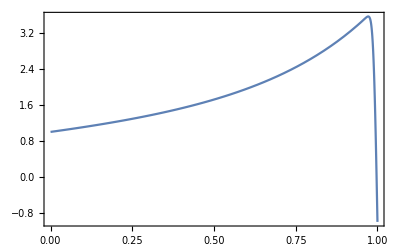

```mathematica
Plot[Ycomp[x]/.eps->0.01,{x,0,1},PlotRange->All,Frame->True]
```

# Question 4

```mathematica
Yapprox11[x_]:=((1-Erf[(x-1)/delta])*(x+Log[1-x]+1))/2
```

```mathematica
Yapprox11[0]/.delta->0.01
```

1.

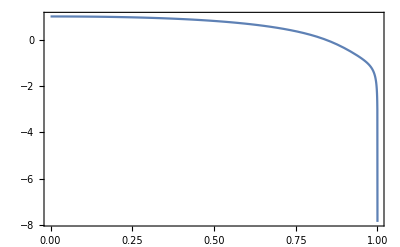

```mathematica
A1=Plot[Yapprox11[x]/.delta->0.1,{x,0,1},PlotRange->All,Frame->True]
```

```mathematica
Yapprox22[x_]:=(-(-1-Erf[(x-1)/delta])(x+Log[x-1]-1))/2
```

```mathematica
Yapprox22[2]/.delta->0.01
```

1.

```mathematica
Yapprox22[1]/.delta->0.1
```

-∞

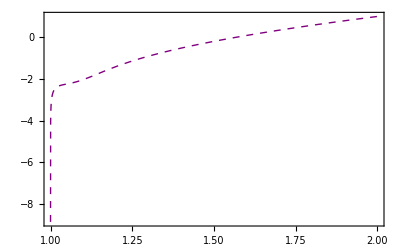

```mathematica
A2=Plot[Yapprox22[x]/.delta->0.1,{x,1,2},PlotRange->All,Frame->True,PlotStyle->{Dashed,Purple,Thick}]
```

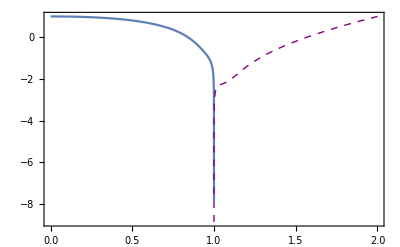

```mathematica
Show[A1,A2]
```

# Question 5

```mathematica
Solve[((1-B*Exp[1])/(B*Exp[-1]+1))==Exp[-2],B]
```

{{B→(ⅇ-ⅇ^3)/(-1-ⅇ^4)}}

```mathematica
FullSimplify[(ⅇ-ⅇ^3)/(-1-ⅇ^4)]
```

(ⅇ (-1+ⅇ^2))/(1+ⅇ^4)

```mathematica
N[(ⅇ (-1+ⅇ^2))/(1+ⅇ^4)]
```

0.312371

## NEW STUFF

```mathematica
Integrate[Sqrt[Pi]Exp[-s^2]Erfi[s],{s,0,X}]
```

X^2 HypergeometricPFQ[{1,1},{3/2,2},-X^2]

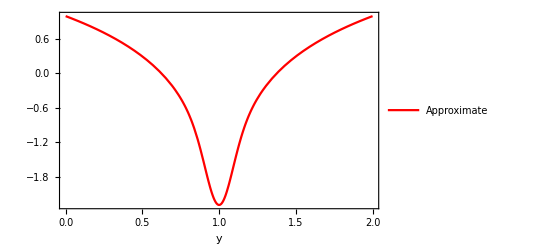

```mathematica
Plot[1+Log[delta]-B+((x-1)/delta)^2 HypergeometricPFQ[{1,1},{3/2,2},-((x-1)/delta)^2]/.{delta->0.1,B->0.99},{x,0,2},PlotStyle->{Red,Thick},PlotRange->All,Frame->True,FrameLabel->y,PlotLegends->{Approximate}]
```

# Question 7

## b)

```mathematica
uap[y_]:=(U/L)y+eps*(U/2)*(((y^2)/L)-y)
```

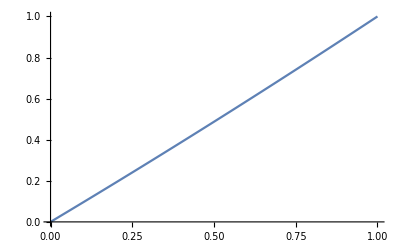

```mathematica
Aprox=Plot[uap[y]/.{eps->0.1,U->1,L->1},{y,0,1}]
```

```mathematica
DSolve[{u''[y]==eps*u'[y],u[0]==0,u[1]==1},u[y],y]
```

{{u[y]→(-1+ⅇ^(eps y))/(-1+ⅇ^eps)}}

```mathematica
uex[y_]:=(-1+ⅇ^(eps y))/(-1+ⅇ^eps)
```

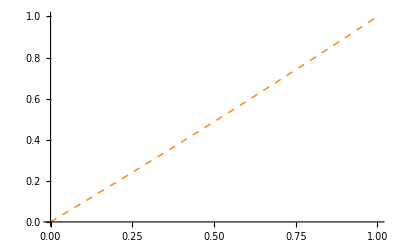

```mathematica
Exact=Plot[uex[y]/.eps->0.1,{y,0,1},PlotStyle->{Dashed,Thick,Orange}]
```

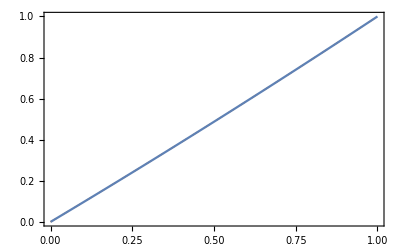

```mathematica
Show[Exact,Aprox,PlotRange->All,Frame->True]
```

## c)

## BLT Approximate

```mathematica
uBLT[y_]:=U*Exp[(y-1)/(d)]
```

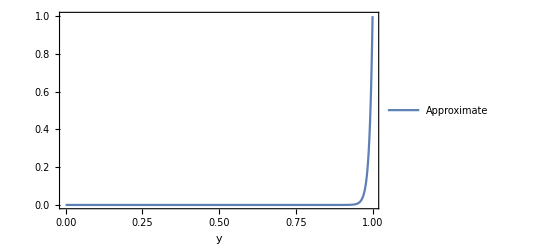

```mathematica
Plot1=Plot[uBLT[y]/.{U->1,d->0.01},{y,0,1},PlotRange->All,Frame->True,PlotLegends->{Approximate},FrameLabel->y]
```

## BLT Exact

```mathematica
DSolve[{delta*uf''[y]==uf'[y],uf[L]==U,uf[0]==0},uf[y],y]
```

{{uf[y]→((-1+ⅇ^(y/delta)) U)/(-1+ⅇ^(L/delta))}}

```mathematica
uf[y_]:=((-1+ⅇ^(y/delta)) U)/(-1+ⅇ^(L/delta));
```

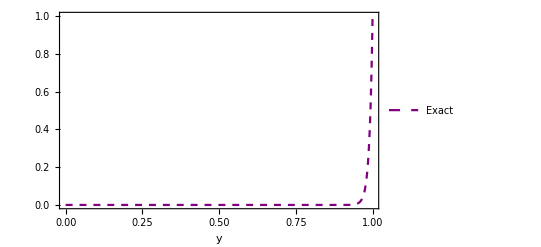

```mathematica
Plot2=Plot[uf[y]/.{delta->0.01,U->1,L->1},{y,0,1},PlotRange->All,Frame->True,PlotStyle->{Purple,Thick,Dashed},PlotLegends->{Exact},FrameLabel->y]
```

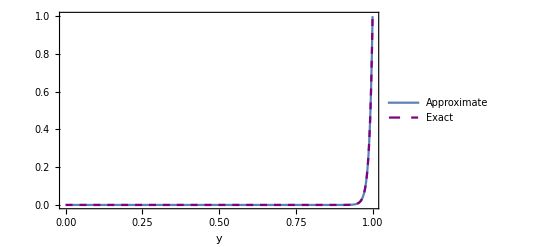

```mathematica
Show[Plot1,Plot2,FrameLabel->y]
```